```mathematica
m=9;
```

Create a m x m central difference matrix

```mathematica
A =DiagonalMatrix[ConstantArray[-1,m-1],-1,m]+DiagonalMatrix[ConstantArray[1,m-1],1,m];
A[[1,m]] = -1;
A[[m,1]] = 1;
A //MatrixForm
(* ν = a k/(2h) *)
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1
-1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

```mathematica
Differences[{a,b,c,d}]
```

{-a+b,-b+c,-c+d}

```mathematica
Differences@Numerator[Inverse[IdentityMatrix[Length[A]]+ν A][[1]]][[2;;;;2]]
```

{ν+5 ν^3+6 ν^5+ν^6+ν^7,ν^3+ν^4+3 ν^5+2 ν^6+ν^7,ν^2+4 ν^4+ν^5+3 ν^6+ν^7}

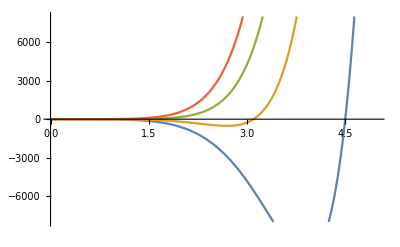

```mathematica
Plot[Evaluate@Numerator[Inverse[IdentityMatrix[Length[A]]+ν A][[1]]][[2;;;;2]],{ν,0,5},PlotRange->{-8000,8000}]
```

Check if there exists a value ν =  a k/(2h) > 0 such that entries of (I + (νA))^-1 are positive. 
The following checks if each off-diagonal entries of  (I + (νA))^-1 can be possitive for certain values of ν.
If False is returned, then that means that there is at least a negative off-diagonal entry in  (I + (νA))^-1 for any ν>0

```mathematica
BE = Inverse[IdentityMatrix[Length[A]]+ν A];
listall = Table[Reduce[{BE[[i,j]]≥ 0,ν>0},ν,Reals],{i,1,m},{j,1,m}];
listoffdiag = Table[If[i≠ j,Reduce[{BE[[i,j]]≥ 0,ν>0},ν,Reals]],{i,1,m},{j,1,m}];
DeleteCases[DeleteDuplicates[Join@@listall],Null]
DeleteCases[DeleteDuplicates[Join@@listoffdiag],Null]
```

{ν>0,ν≥Root[-1-6 #1^2-10 #1^4-4 #1^6+#1^7&,1],ν≥Root[-1-3 #1^2+#1^3&,1]}

{ν≥Root[-1-6 #1^2-10 #1^4-4 #1^6+#1^7&,1],ν>0,ν≥Root[-1-3 #1^2+#1^3&,1]}

Non-repeated off-diagonal entries of (I + (νA))^-1:

```mathematica
DeleteCases[DeleteDuplicates[Join@@Table[If[i≠ j,BE[[i,j]]],{i,1,m},{j,1,m}]],Null]//Simplify
```

{-(ν+6 ν^3+10 ν^5+4 ν^7-ν^8)/(1+9 ν^2+27 ν^4+30 ν^6+9 ν^8),(ν^2+5 ν^4+6 ν^6+ν^7+ν^8)/(1+9 ν^2+27 ν^4+30 ν^6+9 ν^8),(ν^3 (-1-4 ν^2+ν^3-3 ν^4+ν^5))/(1+9 ν^2+27 ν^4+30 ν^6+9 ν^8),(ν^4 (1+ν+3 ν^2+2 ν^3+ν^4))/(1+9 ν^2+27 ν^4+30 ν^6+9 ν^8),(ν^4 (1-ν+3 ν^2-2 ν^3+ν^4))/(1+9 ν^2+27 ν^4+30 ν^6+9 ν^8),(ν^3+4 ν^5+ν^6+3 ν^7+ν^8)/(1+9 ν^2+27 ν^4+30 ν^6+9 ν^8),(ν^2+5 ν^4+6 ν^6-ν^7+ν^8)/(1+9 ν^2+27 ν^4+30 ν^6+9 ν^8),(ν+6 ν^3+10 ν^5+4 ν^7+ν^8)/(1+9 ν^2+27 ν^4+30 ν^6+9 ν^8)}

One can see that if m is even, then there exists a negative entry in (I + (νA))^-1 for ν > 0.
But if m is odd, then we can obtain a lower bound on ν such that all off-diagonal entries are positive. If some matrix entries have numerators that attain negative values, then admissible values of ν for positivity depend on roots of the numerator.

Check the same in the case of explicit Euler, i.e positivity of I-νA. Obviously this is not true for any value of m.

```mathematica
FE = IdentityMatrix[Length[A]]-ν A;
listall = Table[Reduce[{FE[[i,j]]≥ 0,ν>0},ν,Reals],{i,1,m},{j,1,m}];
listoffdiag = Table[If[i≠ j,Reduce[{FE[[i,j]]≥ 0,ν>0},ν,Reals]],{i,1,m},{j,1,m}];
DeleteCases[DeleteDuplicates[Join@@listall],Null]
DeleteCases[DeleteDuplicates[Join@@listoffdiag],Null]//Simplify
```

{ν>0,False}

{False,ν>0}

```mathematica
cDiffMat[m_]:=SparseArray[{Band[{1,2}]->1,Band[{2,1}]->-1,Band[{1,m}]->-1,Band[{m,1}]->1},{m,m}]
```

```mathematica
idPluscDiffMat[m_]:=IdentityMatrix[m]+ν cDiffMat[m]
```

```mathematica
inverse[m_]:=Inverse[IdentityMatrix[m]+ν cDiffMat[m]]
```

```mathematica
det[m_]:=Det[IdentityMatrix[m]+ν cDiffMat[m]]
```

### The det seems to be always a positive polynomial:

```mathematica
Table[det[m],{m,2,20}]
```

{1+ν^2,1+3 ν^2,1+4 ν^2,1+5 ν^2+5 ν^4,1+6 ν^2+9 ν^4,1+7 ν^2+14 ν^4+7 ν^6,1+8 ν^2+20 ν^4+16 ν^6,1+9 ν^2+27 ν^4+30 ν^6+9 ν^8,1+10 ν^2+35 ν^4+50 ν^6+25 ν^8,1+11 ν^2+44 ν^4+77 ν^6+55 ν^8+11 ν^10,1+12 ν^2+54 ν^4+112 ν^6+105 ν^8+36 ν^10,1+13 ν^2+65 ν^4+156 ν^6+182 ν^8+91 ν^10+13 ν^12,1+14 ν^2+77 ν^4+210 ν^6+294 ν^8+196 ν^10+49 ν^12,1+15 ν^2+90 ν^4+275 ν^6+450 ν^8+378 ν^10+140 ν^12+15 ν^14,1+16 ν^2+104 ν^4+352 ν^6+660 ν^8+672 ν^10+336 ν^12+64 ν^14,1+17 ν^2+119 ν^4+442 ν^6+935 ν^8+1122 ν^10+714 ν^12+204 ν^14+17 ν^16,1+18 ν^2+135 ν^4+546 ν^6+1287 ν^8+1782 ν^10+1386 ν^12+540 ν^14+81 ν^16,1+19 ν^2+152 ν^4+665 ν^6+1729 ν^8+2717 ν^10+2508 ν^12+1254 ν^14+285 ν^16+19 ν^18,1+20 ν^2+170 ν^4+800 ν^6+2275 ν^8+4004 ν^10+4290 ν^12+2640 ν^14+825 ν^16+100 ν^18}

### Number of different numerators in the inverse:

```mathematica
Table[Length@Union@Flatten@(inverse[m] det[m]) ,{m,2,20}]
```

{3,3,4,5,5,7,7,9,8,11,29,25,19,29,49,33,42,37,52}

### For EVEN m: the second element in the first row seems always to be a negative polynomial: cf. the last element in the same row. The proof should follow from this.

```mathematica
Table[(inverse[m] )[[1,2]],{m,2,10,2}]
```

{-ν/(1+ν^2),-ν/(1+4 ν^2),(-ν-3 ν^3)/(1+6 ν^2+9 ν^4),(-ν-5 ν^3-6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν-7 ν^3-15 ν^5-10 ν^7)/(1+10 ν^2+35 ν^4+50 ν^6+25 ν^8)}

```mathematica
Table[(inverse[m] )[[1,m]],{m,2,10,2}]
```

{-ν/(1+ν^2),ν/(1+4 ν^2),(ν+3 ν^3)/(1+6 ν^2+9 ν^4),(ν+5 ν^3+6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν+7 ν^3+15 ν^5+10 ν^7)/(1+10 ν^2+35 ν^4+50 ν^6+25 ν^8)}

### For ODD m: the lower positive bound for ν seems to be determined by the (1,2) polynomial:

```mathematica
Table[MatrixForm[inverse[m] det[m]][[1,1,2]],{m,3,19,2}]
```

```mathematica
{-ν+ν^2,-ν-2 ν^3+ν^4,-ν-4 ν^3-3 ν^5+ν^6,-ν-6 ν^3-10 ν^5-4 ν^7+ν^8,-ν-8 ν^3-21 ν^5-20 ν^7-5 ν^9+ν^10,ν (-1-10 ν^2-36 ν^4-56 ν^6-35 ν^8-6 ν^10+ν^11),ν (-1-12 ν^2-55 ν^4-120 ν^6-126 ν^8-56 ν^10-7 ν^12+ν^13),ν (-1-14 ν^2-78 ν^4-220 ν^6-330 ν^8-252 ν^10-84 ν^12-8 ν^14+ν^15),ν (-1-16 ν^2-105 ν^4-364 ν^6-715 ν^8-792 ν^10-462 ν^12-120 ν^14-9 ν^16+ν^17)}//Factor
```

{(-1+ν) ν,ν (-1-2 ν^2+ν^3),ν (-1-4 ν^2-3 ν^4+ν^5),ν (-1-6 ν^2-10 ν^4-4 ν^6+ν^7),ν (-1-8 ν^2-21 ν^4-20 ν^6-5 ν^8+ν^9),ν (-1-10 ν^2-36 ν^4-56 ν^6-35 ν^8-6 ν^10+ν^11),ν (-1-12 ν^2-55 ν^4-120 ν^6-126 ν^8-56 ν^10-7 ν^12+ν^13),ν (-1-14 ν^2-78 ν^4-220 ν^6-330 ν^8-252 ν^10-84 ν^12-8 ν^14+ν^15),ν (-1-16 ν^2-105 ν^4-364 ν^6-715 ν^8-792 ν^10-462 ν^12-120 ν^14-9 ν^16+ν^17)}

```mathematica
-CoefficientList[-1-16 ν^2-105 ν^4-364 ν^6-715 ν^8-792 ν^10-462 ν^12-120 ν^14-9 ν^16+ν^17,ν]
```

{1,0,16,0,105,0,364,0,715,0,792,0,462,0,120,0,9,-1}

### These elements satisfy the following recursion:

```mathematica
FindLinearRecurrence[{(-1+ν) ν,ν (-1-2 ν^2+ν^3),ν (-1-4 ν^2-3 ν^4+ν^5),ν (-1-6 ν^2-10 ν^4-4 ν^6+ν^7),ν (-1-8 ν^2-21 ν^4-20 ν^6-5 ν^8+ν^9),ν (-1-10 ν^2-36 ν^4-56 ν^6-35 ν^8-6 ν^10+ν^11),ν (-1-12 ν^2-55 ν^4-120 ν^6-126 ν^8-56 ν^10-7 ν^12+ν^13),ν (-1-14 ν^2-78 ν^4-220 ν^6-330 ν^8-252 ν^10-84 ν^12-8 ν^14+ν^15),ν (-1-16 ν^2-105 ν^4-364 ν^6-715 ν^8-792 ν^10-462 ν^12-120 ν^14-9 ν^16+ν^17)}]
```

{1+3 ν^2,-ν^2-3 ν^4,ν^6}

```mathematica
1/ν{(-1+ν) ν,ν (-1-2 ν^2+ν^3),ν (-1-4 ν^2-3 ν^4+ν^5),ν (-1-6 ν^2-10 ν^4-4 ν^6+ν^7),ν (-1-8 ν^2-21 ν^4-20 ν^6-5 ν^8+ν^9),ν (-1-10 ν^2-36 ν^4-56 ν^6-35 ν^8-6 ν^10+ν^11),ν (-1-12 ν^2-55 ν^4-120 ν^6-126 ν^8-56 ν^10-7 ν^12+ν^13),ν (-1-14 ν^2-78 ν^4-220 ν^6-330 ν^8-252 ν^10-84 ν^12-8 ν^14+ν^15),ν (-1-16 ν^2-105 ν^4-364 ν^6-715 ν^8-792 ν^10-462 ν^12-120 ν^14-9 ν^16+ν^17)}
```

{-1+ν,-1-2 ν^2+ν^3,-1-4 ν^2-3 ν^4+ν^5,-1-6 ν^2-10 ν^4-4 ν^6+ν^7,-1-8 ν^2-21 ν^4-20 ν^6-5 ν^8+ν^9,-1-10 ν^2-36 ν^4-56 ν^6-35 ν^8-6 ν^10+ν^11,-1-12 ν^2-55 ν^4-120 ν^6-126 ν^8-56 ν^10-7 ν^12+ν^13,-1-14 ν^2-78 ν^4-220 ν^6-330 ν^8-252 ν^10-84 ν^12-8 ν^14+ν^15,-1-16 ν^2-105 ν^4-364 ν^6-715 ν^8-792 ν^10-462 ν^12-120 ν^14-9 ν^16+ν^17}

```mathematica
FindLinearRecurrence[{-1+ν,-1-2 ν^2+ν^3,-1-4 ν^2-3 ν^4+ν^5,-1-6 ν^2-10 ν^4-4 ν^6+ν^7,-1-8 ν^2-21 ν^4-20 ν^6-5 ν^8+ν^9,-1-10 ν^2-36 ν^4-56 ν^6-35 ν^8-6 ν^10+ν^11,-1-12 ν^2-55 ν^4-120 ν^6-126 ν^8-56 ν^10-7 ν^12+ν^13,-1-14 ν^2-78 ν^4-220 ν^6-330 ν^8-252 ν^10-84 ν^12-8 ν^14+ν^15,-1-16 ν^2-105 ν^4-364 ν^6-715 ν^8-792 ν^10-462 ν^12-120 ν^14-9 ν^16+ν^17}]
```

{1+3 ν^2,-ν^2-3 ν^4,ν^6}

```mathematica
RecurrenceTable[{second[n+3]==(1+3 ν^2)second[n+2]-(ν^2+3 ν^4) second[n+1]+ν^6 second[n],second[1]==-1+ν,second[2]==-1-2 ν^2+ν^3,second[3]==-1-4 ν^2-3 ν^4+ν^5},second,{n,1,9}]//Expand
```

{-1+ν,-1-2 ν^2+ν^3,-1-4 ν^2-3 ν^4+ν^5,-1-6 ν^2-10 ν^4-4 ν^6+ν^7,-1-8 ν^2-21 ν^4-20 ν^6-5 ν^8+ν^9,-1-10 ν^2-36 ν^4-56 ν^6-35 ν^8-6 ν^10+ν^11,-1-12 ν^2-55 ν^4-120 ν^6-126 ν^8-56 ν^10-7 ν^12+ν^13,-1-14 ν^2-78 ν^4-220 ν^6-330 ν^8-252 ν^10-84 ν^12-8 ν^14+ν^15,-1-16 ν^2-105 ν^4-364 ν^6-715 ν^8-792 ν^10-462 ν^12-120 ν^14-9 ν^16+ν^17}

```mathematica
%29==%37
```

True

```mathematica
RSolve[{second[n+3]==(1+3 ν^2)second[n+2]-(ν^2+3 ν^4) second[n+1]+ν^6 second[n],second[1]==-1+ν,second[2]==-1-2 ν^2+ν^3,second[3]==-1-4 ν^2-3 ν^4+ν^5},second[n],n]
```

{{second[n]→(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))}}

### This is an explicit formula for the polynomials which (if the element (1,2) has the smallest positive root) determine the smallest possible ν>0 value.

```mathematica
Table[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2)),{n,1,6}]//Simplify
```

{-1+ν,-1-2 ν^2+ν^3,-1-4 ν^2-3 ν^4+ν^5,-1-6 ν^2-10 ν^4-4 ν^6+ν^7,-1-8 ν^2-21 ν^4-20 ν^6-5 ν^8+ν^9,-1-10 ν^2-36 ν^4-56 ν^6-35 ν^8-6 ν^10+ν^11}

```mathematica
N[Table[Reduce[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))>0],{n,1,15}],20]
```

{ν>1.,ν>2.2055694304005903117,ν>3.3617657267144615732,ν>4.5069633965305057749,ν>5.6478748967865146115,ν>6.7866658033191965387,ν>7.9242514529216698125,ν>9.0610861788817023851,ν>10.197421287623980626,ν>11.333407136290336656,ν>12.469139220581783219,ν>13.604681115388041778,ν>14.740076788426239465,ν>15.875357620320218936,ν>17.010546609277172976}

```mathematica
N[Table[Reduce[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))>0],{n,1,30}],20]
```

{ν>1.,ν>2.2055694304005903117,ν>3.3617657267144615732,ν>4.5069633965305057749,ν>5.6478748967865146115,ν>6.7866658033191965387,ν>7.9242514529216698125,ν>9.0610861788817023851,ν>10.197421287623980626,ν>11.333407136290336656,ν>12.469139220581783219,ν>13.604681115388041778,ν>14.740076788426239465,ν>15.875357620320218936,ν>17.010546609277172976,ν>18.145660995444771567,ν>19.280713957200392349,ν>20.41571574103175839,ν>21.550674434065819794,ν>22.685596504521694258,ν>23.820487187558640086,ν>24.955350765775926473,ν>26.090190776465082208,ν>27.225010167001471683,ν>28.359811412910516288,ν>29.494596608666797425,ν>30.629367538301192434,ν>31.764125730867927873,ν>32.898872504428665255,ν>34.033609001234758888}

```mathematica
N[Table[Reduce[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))>0],{n,30,60}],20]
```

{ν>34.033609001234758888,ν>35.168336216096426329,ν>36.303055019430056786,ν>37.437766176113149008,ν>38.572470361010452672,ν>39.707168171837390887,ν>40.841860139878747892,ν>41.976546738968555037,ν>43.111228393051609298,ν>44.245905482581299925,ν>45.38057834995746271,ν>46.515247304168215711,ν>47.649912624768489365,ν>48.784574565303264399,ν>49.919233356263885581,ν>51.053889207650104395,ν>52.188542311197864561,ν>53.32319284232262617,ν>54.457840961819722616,ν>55.592486817356468085,ν>56.727130544785177138,ν>57.861772269301682388,ν>58.996412106470152966,ν>60.131050163131875668,ν>61.26568653821304359,ν>62.400321323444408192,ν>63.534954604003813861,ν>64.669586459091087154,ν>65.804216962443446183,ν>66.93884618279848819,ν>68.073474184310872153}

```mathematica
34.03360900123475888770913034175562334767/30
```

1.13445363337449196292363767805852077826

```mathematica
68.07347418431087215348834144841752375271/60
```

1.13455790307184786922480569080695872921

# Normalized by n:

```mathematica
N[Table[Reduce[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))>0]/.(ν>a_->a/n),{n,2,40}],20]
```

{1.1027847152002951559,1.1205885755714871911,1.1267408491326264437,1.1295749793573029223,1.1311109672198660898,1.1320359218459528304,1.1326357723602127981,1.1330468097359978473,1.1333407136290336656,1.1335581109619802926,1.1337234262823368148,1.1338520606481722666,1.1339541157371584954,1.1340364406184781984,1.1341038122152982229,1.13415964454119955,1.1342064300573199106,1.1342460228455694629,1.1342798252260847129,1.1343089136932685755,1.1343341257170875669,1.1343561207158731395,1.1343754236250613201,1.1343924565164206515,1.134407561871799901,1.1344210199370812013,1.1344330618167117097,1.1344438794630574226,1.1344536333744919629,1.134462458583755688,1.1344704693571892746,1.1344777629125196669,1.1344844223826603727,1.1344905191953540253,1.1344961149966318859,1.1345012632153663523,1.1345060103434634026,1.1345103969892641006,1.1345144587489365677}

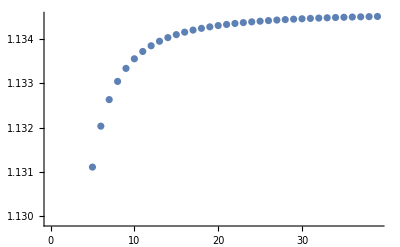

```mathematica
ListPlot[%]
```

```mathematica
N[Table[Reduce[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))>0]/.(ν>a_->a/n),{n,41,60}],20]
```

{1.1345182269309320905,1.1345217291611545087,1.1345249898907735907,1.1345280308241792177,1.134530871281113431,1.1345335285043014035,1.1345360179217580036,1.1345383533712442212,1.1345405472929891446,1.1345426108957035428,1.134544554300032988,1.134546386662887557,1.1345481162855070881,1.1345497507076489554,1.1345512967898983308,1.1345527607857823904,1.1345541484051067922,1.1345554648697145894,1.1345567149626862405,1.1345579030718478692}

```mathematica
N[Table[Reduce[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))>0]/.(ν>a_->a/n),{n,61,80}],20]
```

{1.1345590332283280475,1.1345601091407967957,1.1345611342259306921,1.1345621116355721056,1.1345630442809862657,1.1345639348545652579,1.1345647858492814901,1.1345655995761534333,1.1345663781799524117,1.1345671236533500163,1.1345678378496805964,1.1345685224944716326,1.1345691791958760836,1.1345698094541246038,1.1345704146701014753,1.1345709961531358844,1.1345715551280895288,1.1345720927418122628,1.1345726100690293665,1.1345731081177169199}

```mathematica
2^n ν^(2n-1) √(1+4 ν^2)+ (1+2 ν^2-√(1+4 ν^2))^n- (1+2 ν^2+√(1+4 ν^2))^n/.ν->n
```

2^n n^(-1+2 n) √(1+4 n^2)+(1+2 n^2-√(1+4 n^2))^n-(1+2 n^2+√(1+4 n^2))^n

### Conjecture: at ν=n is is still negative

```mathematica
Table[2^n n^(-1+2 n) √(1+4 n^2)+(1+2 n^2-√(1+4 n^2))^n-(1+2 n^2+√(1+4 n^2))^n,{n,1,10}]//N
```

{0.,-16.4924,-1800.5,-342743.,-1.04784×10^8,-4.73543×10^10,-2.97497×10^13,-2.48235×10^16,-2.65691×10^19,-3.54939×10^22}

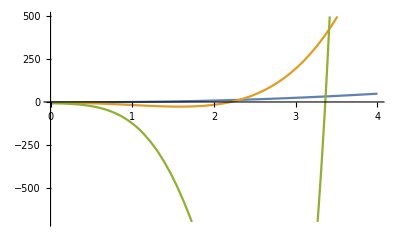

```mathematica
Plot[Evaluate@Factor@Table[2^n ν^(2n-1) √(1+4 ν^2)+ (1+2 ν^2-√(1+4 ν^2))^n- (1+2 ν^2+√(1+4 ν^2))^n,{n,3}],{ν,0,4}]
```

```mathematica
(2^n ν^(2n-1) √(1+4 ν^2))/((1+2 ν^2+√(1+4 ν^2))^n)+ ((1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2)))^n== 1
```

```mathematica
((1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2)))^n+2^n ν^(-1+2 n) √(1+4 ν^2) (1+2 ν^2+√(1+4 ν^2))^-n==1
```

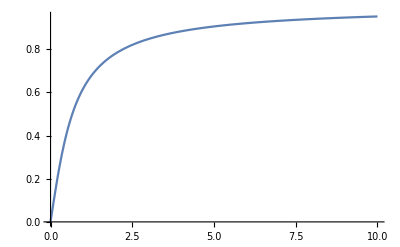

```mathematica
Plot[((1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2)))^(1/4),{ν,0,10},PlotRange->All]
```

```mathematica
Reduce[1>(1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2))>0]
```

ν<0||ν>0

```mathematica
Reduce[x==(1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2))&&ν>0,ν,Reals]
```

0<x<1&&ν==Root[-x-4 x #1^2+(1-2 x+x^2) #1^4&,2]

```mathematica
Root[-x-4 x #1^2+(1-2 x+x^2) #1^4&,2]//RootReduce
```

Root[-x-4 x #1^2+(1-2 x+x^2) #1^4&,2]

```mathematica
-x-4 x #1^2+(1-2 x+x^2) #1^4&[X]
```

```mathematica
Solve[-x-4 x X^2+(1-2 x+x^2) X^4==0,X]
```

{{X→-√((2 x)/(1-2 x+x^2)-(√(x (1+x)^2))/(1-2 x+x^2))},{X→√((2 x)/(1-2 x+x^2)-(√(x (1+x)^2))/(1-2 x+x^2))},{X→-√((2 x)/(1-2 x+x^2)+(√(x (1+x)^2))/(1-2 x+x^2))},{X→√((2 x)/(1-2 x+x^2)+(√(x (1+x)^2))/(1-2 x+x^2))}}

```mathematica
FullSimplify[√((2 x)/(1-2 x+x^2)+(√(x (1+x)^2))/(1-2 x+x^2)),0<x<1]
```

1/(1/x^(1/4)-x^(1/4))

```mathematica
x^n+2^n ν^(-1+2 n) √(1+4 ν^2) (1+2 ν^2+√(1+4 ν^2))^-n==1/.ν->1/(1/x^(1/4)-x^(1/4))
```

```mathematica
2^n (1+√((1+√x)^2/(-1+√x)^2)+(2 √x)/(-1+√x)^2)^-n √((1+√x)^2/(-1+√x)^2) (1/(1/x^(1/4)-x^(1/4)))^(-1+2 n)+x^n==1
```

```mathematica
Simplify[2^n (1+√((1+√x)^2/(-1+√x)^2)+(2 √x)/(-1+√x)^2)^-n √((1+√x)^2/(-1+√x)^2) (1/(1/x^(1/4)-x^(1/4)))^(-1+2 n)+x^n==1,0<x<1]
```

### By using the new variable x==(1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2))∈(0,1), we’ve transformed the equation to

```mathematica
(1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2))==(1+4 ν^2+2 ν^4-√(1+4 ν^2)-2 ν^2 √(1+4 ν^2))/(2 ν^4)
```

```mathematica
((-1+√(1+4 ν^2))/(2 ν))^4==((1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2)))//Simplify
```

True

### Remark: (1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2))=((-1+√(1+4 ν^2))/(2 ν))^4.

```mathematica
(1+√x) x^(-1/4+n/2)+x^n==1
```

```mathematica
x^(-1/4+n/2)+x^(1/4+n/2)+x^n==1/.x->y^4//PowerExpand
```

y^(4 (-1/4+n/2))+y^(4 (1/4+n/2))+y^(4 n)==1

### By using the new variable y==((1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2)))^(1/4)=(-1+√(1+4 ν^2))/(2 ν)∈(0,1), we’ve transformed the equation to

```mathematica
y^(-1+2 n)+y^(1+2 n)+y^(4 n)==1
```

y^(4 n)+y^(-1+2 n)+y^(1+2 n)==1

```mathematica
Table[Factor[y^(4 n)+y^(-1+2 n)+y^(1+2 n)-1],{n,1,10}]
```

{(1+y^2) (-1+y+y^2),(1+y^2) (-1+y^2+y^3-y^4+y^6),(1+y^2) (-1+y^2-y^4+y^5+y^6-y^8+y^10),(1+y^2) (-1+y^2-y^4+y^6+y^7-y^8+y^10-y^12+y^14),(1+y^2) (-1+y^2-y^4+y^6-y^8+y^9+y^10-y^12+y^14-y^16+y^18),(1+y^2) (-1+y^2-y^4+y^6-y^8+y^10+y^11-y^12+y^14-y^16+y^18-y^20+y^22),(1+y^2) (-1+y^2-y^4+y^6-y^8+y^10-y^12+y^13+y^14-y^16+y^18-y^20+y^22-y^24+y^26),(1+y^2) (-1+y^2-y^4+y^6-y^8+y^10-y^12+y^14+y^15-y^16+y^18-y^20+y^22-y^24+y^26-y^28+y^30),(1+y^2) (-1+y^2-y^4+y^6-y^8+y^10-y^12+y^14-y^16+y^17+y^18-y^20+y^22-y^24+y^26-y^28+y^30-y^32+y^34),(1+y^2) (-1+y^2-y^4+y^6-y^8+y^10-y^12+y^14-y^16+y^18+y^19-y^20+y^22-y^24+y^26-y^28+y^30-y^32+y^34-y^36+y^38)}

```mathematica
Factor[y^(4 n)+y^(-1+2 n)]
```

y^(-1+2 n) (1+y^(1+2 n))

```mathematica
Factor[y^(-1+2 n)+y^(1+2 n)]
```

y^(-1+2 n) (1+y^2)

```mathematica
Factor[y^(4 n)+y^(-1+2 n)+y^(1+2 n)+1]
```

```mathematica
((y+y^(2 n)) (1+y^(1+2 n)))/y==2
```

```mathematica
N[Table[Reduce[(1+y^(2 n-1)) (1+y^(1+2 n))==2&&y>0,Reals],{n,1,20}],20]
```

{y==0.6180339887498948482,y==0.79867542669801596634,y==0.86226864572027366287,y==0.89519551987618072583,y==0.91538215950178433457,y==0.92903636784836729921,y==0.93889122377637678947,y==0.94634029295423037049,y==0.95216934321796380544,y==0.95685533788053513055,y==0.96070464302774625783,y==0.96392307306741436406,y==0.96665403012276758086,y==0.96900050222124924157,y==0.97103836722468706446,y==0.97282476466198179279,y==0.97440354499824022014,y==0.97580892142353154014,y==0.97706797996721753308,y==0.97820244379560241066}

```mathematica
Solve[((1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2)))^(1/4)==0.97820244379560241065763810676540942144]
```

{{ν→-22.685596504521694257886531004044688},{ν→-0.49987859923669988428120689405045557 ⅈ},{ν→0.49987859923669988428120689405045557 ⅈ},{ν→22.685596504521694257886531004044688}}

```mathematica
Solve[((1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2)))^(1/4)==y,ν]
```

```mathematica
{{ν->-y/(-1+y^2)},{ν->y/(-1+y^2)},{ν->-y/(√(-1-2 y^2-y^4))},{ν->y/(√(-1-2 y^2-y^4))}}/.y->0.97820244379560241065763810676540942144
```

{{ν→22.6855965045216942578865310040446876},{ν→-22.6855965045216942578865310040446876},{ν→0.4998785992366998842812068940504555653 ⅈ},{ν→-0.4998785992366998842812068940504555653 ⅈ}}

### The inverse transformation (from y to ν): ν→y/(1-y^2).

```mathematica
Solve[ν==y/(1-y^2),y]
```

{{y→(-1-√(1+4 ν^2))/(2 ν)},{y→(-1+√(1+4 ν^2))/(2 ν)}}

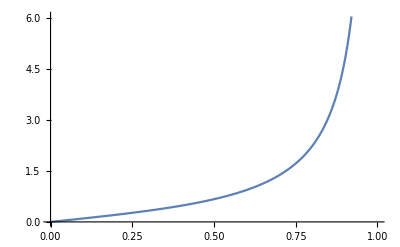

```mathematica
Plot[y/(1-y^2),{y,0,1}]
```

```mathematica
N[Table[Reduce[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))>0],{n,20,20}],20]
```

{ν>22.685596504521694258}

```mathematica
N[Table[Reduce[y^(4 n)+y^(-1+2 n)+y^(1+2 n)==1&&y>0,Reals],{n,1,20}],20]
```

{y==0.6180339887498948482,y==0.79867542669801596634,y==0.86226864572027366287,y==0.89519551987618072583,y==0.91538215950178433457,y==0.92903636784836729921,y==0.93889122377637678947,y==0.94634029295423037049,y==0.95216934321796380544,y==0.95685533788053513055,y==0.96070464302774625783,y==0.96392307306741436406,y==0.96665403012276758086,y==0.96900050222124924157,y==0.97103836722468706446,y==0.97282476466198179279,y==0.97440354499824022014,y==0.97580892142353154014,y==0.97706797996721753308,y==0.97820244379560241066}

```mathematica
%203==%206
```

True

```mathematica
Root[-1+#1^2-#1^4+#1^5+#1^6-#1^8+#1^10&,2]//N
```

0.862269

```mathematica
Root[-1+#1^2-#1^4+#1^6-#1^8+#1^9+#1^10-#1^12+#1^14-#1^16+#1^18&,1]//N
```

-1.09244

```mathematica
Root[-1+#1^2-#1^4+#1^6-#1^8+#1^9+#1^10-#1^12+#1^14-#1^16+#1^18&,2]//N
```

0.915382

```mathematica
1/0.9153821595017844
```

1.09244

```mathematica
y-1/y//Together
```

(-1+y^2)/y

```mathematica
Reduce[0<(-1+√(1+4 ν^2))/(2 ν)<1]
```

ν>0

### So it seems simpler to investigate the roots of the equation y^(4 n)+y^(-1+2 n)+y^(1+2 n)==1

### or, in other words, the equation (1+y^(2 n-1)) (1+y^(1+2 n))==2.

### We know that 0<y<1. Hence we are to find positive roots. From the 1st form it is clear (due to strict monotonicity) that we have a unique positive y-root. Due to ν=y/(1-y^2), this means that we have a unique ν-root.

```mathematica
Solve[Z^2+1/y Z+y Z==1,Z]
```

{{Z→1/2 (-1/y-y-√(6+1/y^2+y^2))},{Z→1/2 (-1/y-y+√(6+1/y^2+y^2))}}

```mathematica
Solve[n==y/(1-y^2),y]
```

{{y→(-1-√(1+4 n^2))/(2 n)},{y→(-1+√(1+4 n^2))/(2 n)}}

```mathematica
Series[(-1+√(1+4 n^2))/(2 n),{n,∞,3}]
```

1-1/(2 n)+1/(8 n^2)+O[1/n]^4

```mathematica
Limit[(1-1/(2n))^(2n),n->∞]
```

1/ⅇ

```mathematica
1+1/E//N
```

1.36788

### Heuristically: when y is close to one, the 2 factors in (1+y^(2 n-1)) (1+y^(1+2 n))==2 are approx. equal. So

```mathematica
y==(√2-1)^(1/(2n))
```

```mathematica
Series[(√2-1)^(1/(2n)),{n,∞,3}]//Normal
```

```mathematica
1+Log[-1+√2]/(2 n)+Log[-1+√2]^2/(8 n^2)+Log[-1+√2]^3/(48 n^3)//N
```

1.-0.0142639/n^3+0.0971024/n^2-0.440687/n

```mathematica
ν==y/(1-y^2)/.y->1+Log[-1+√2]/(2 n)//FullSimplify
```

```mathematica
ν==n (1/ArcSinh[1]+1/(-4 n+ArcSinh[1]))//N
```

ν==(1.13459+1/(0.881374-4. n)) n

### So most probably the first term of the asymptotic expansion of ν is n/ArcSinh[1]==n/Log[1+√2]

```mathematica
N[n/Log[1+√2],20]
```

1.1345926571065109841 n

```mathematica
1.134573108117716919880580380305773292
```

```mathematica
ArcSinh[1]//FunctionExpand
```

ArcSinh[1]

### So we have two bounds for y: 1-(1/2)/n and 1 + Log[-1 + √2]/(2n) =1-Log[√(1+√2)]/n.

```mathematica
Log[-1+√2]/2
```

```mathematica
Log[√(1+√2)]//N
```

0.440687

```mathematica
(1+y^(2 n-1)) (1+y^(1+2 n))/.y->1-(1/2)/n
```

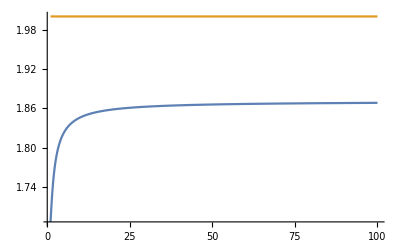

```mathematica
Plot[{(1+(1-1/(2 n))^(-1+2 n)) (1+(1-1/(2 n))^(1+2 n)),2},{n,1,100}]
```

```mathematica
Limit[(1+(1-1/(2 n))^(-1+2 n)) (1+(1-1/(2 n))^(1+2 n)),n->∞]//N
```

1.87109

```mathematica
(1+y^(2 n-1)) (1+y^(1+2 n))/.y->1-Log[√(1+√2)]/n
```

(1+(1-Log[1+√2]/(2 n))^(-1+2 n)) (1+(1-Log[1+√2]/(2 n))^(1+2 n))

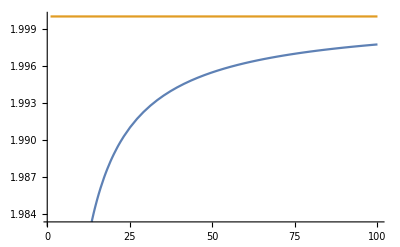

```mathematica
Plot[{(1+(1-Log[1+√2]/(2 n))^(-1+2 n)) (1+(1-Log[1+√2]/(2 n))^(1+2 n)),2},{n,1,100}]
```

```mathematica
Limit[(1+(1-Log[1+√2]/(2 n))^(-1+2 n)) (1+(1-Log[1+√2]/(2 n))^(1+2 n)),n->∞]
```

2

### So it seems that y_n=1-Log[√(1+√2)]/n is an (asymptotically optimal) lower bound. In terms of ν, this is

```mathematica
ν==y/(1-y^2)/.y->1-Log[√(1+√2)]/n//Simplify
```

```mathematica
ν==(4 n^2-2 n Log[1+√2])/(4 n Log[1+√2]-Log[1+√2]^2)//N
```

ν==(-1.76275 n+4. n^2)/(-0.776819+3.52549 n)

### We would like to exclude “bad” ν values. Therefore we give a lower bound for ν.

```mathematica
Reduce[(4 n^2-2 n Log[1+√2])/(4 n Log[1+√2]-Log[1+√2]^2)>(4 n^2-2 n Log[1+√2])/(4 n Log[1+√2])]//N
```

n<0.220343||n>0.440687

```mathematica
(4 n^2-2 n Log[1+√2])/(4 n Log[1+√2])//Simplify
```

```mathematica
-1/2+n/Log[1+√2]//N
```

-0.5+1.13459 n

### So for this value, ν=n/Log[1+√2]-1/2≈1.13459 n -0.5, the polynomial is still negative (provided we prove the inequality (1+(1-Log[1+√2]/(2 n))^(-1+2 n)) (1+(1-Log[1+√2]/(2 n))^(1+2 n))<2):

```mathematica
(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))/.ν->n/Log[1+√2]-1/2//Simplify
```

(2^-n ((1+√(1+4 (-1/2+n/Log[1+√2])^2)+2 (-1/2+n/Log[1+√2])^2)^n (1/2-n/Log[1+√2])+(1-√(1+4 (-1/2+n/Log[1+√2])^2)+2 (-1/2+n/Log[1+√2])^2)^n (-1/2+n/Log[1+√2])+2^n √(1+4 (-1/2+n/Log[1+√2])^2) ((-1/2+n/Log[1+√2])^2)^n))/(√(1+4 (-1/2+n/Log[1+√2])^2) (-1/2+n/Log[1+√2]))

```mathematica
Table[N[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))/.ν->n/Log[1+√2]-1/2,20],{n,1,10}]
```

{-0.36540734289348901594,-1.7224538155851801762,-41.568840608387765238,-2592.0702407208622748,-309799.81955624484032,-6.0617961598032638955×10^7,-1.76291270106982895×10^10,-7.139658203737958622×10^12,-3.8424081041507853732×10^15,-2.6527359242041251619×10^18}

```mathematica
Table[N[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))/.ν->n/Log[1+√2],20],{n,1,10}]
```

{0.13459265710651098406,0.38608955568908627039,6.8557129943914607394,337.28369485868856023,33244.11498795536436,5.531083179487095289×10^6,1.3986764385973714884×10^9,5.0097945898471363974×10^11,2.4165455795500435687×10^14,1.5114715306181484015×10^17}

### And it seems, that the polynomial is already positive for ν=n/Log[1+√2]≈1.13459 n

### For y, this means

```mathematica
(-1+√(1+4 ν^2))/(2 ν)/.ν->n/Log[1+√2]//Simplify
```

```mathematica
(-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/(2 n)//Expand//N
```

```mathematica
(1+y^(2 n-1)) (1+y^(1+2 n))/.y->(-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/(2 n)
```

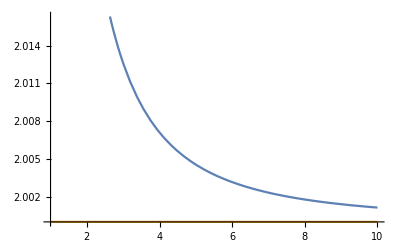

```mathematica
Plot[{(1+2^(1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(-1+2 n)) (1+2^(-1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(1+2 n)),2},{n,1,10}]
```

```mathematica
Limit[(1+2^(1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(-1+2 n)) (1+2^(-1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(1+2 n)),n->∞]
```

2

### Conclusion: if we prove (1+2^(1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(-1+2 n)) (1+2^(-1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(1+2 n))>2

### and (1+(1-Log[1+√2]/(2 n))^(-1+2 n)) (1+(1-Log[1+√2]/(2 n))^(1+2 n))<2, then we have asymptotically optimal lower and upper bounds.

```mathematica
Manipulate[Plot[Evaluate@D[2^n ν^(2n-1) √(1+4 ν^2)+ (1+2 ν^2-√(1+4 ν^2))^n- (1+2 ν^2+√(1+4 ν^2))^n,ν],{ν,0,10},PlotRange->{-100,1000}],{n,1,6,1}]
```

```mathematica
D[2^n ν^(2n-1) √(1+4 ν^2)+ (1+2 ν^2-√(1+4 ν^2))^n- (1+2 ν^2+√(1+4 ν^2))^n,ν]//Simplify
```

```mathematica
(-(4 ν^2 (2^n (-1+2 n) ν^(2 n)+2^(3+n) n ν^(2+2 n)+2 n ν ((1+2 ν^2-√(1+4 ν^2))^n+√(1+4 ν^2) (1+2 ν^2-√(1+4 ν^2))^n+(1+2 ν^2+√(1+4 ν^2))^n-√(1+4 ν^2) (1+2 ν^2+√(1+4 ν^2))^n)))/((-1-2 ν^2+√(1+4 ν^2)) (1+2 ν^2+√(1+4 ν^2))))/(√(1+4 ν^2))
```

```mathematica
(2^n (-1+2 n) ν^(2 n)+2^(3+n) n ν^(2+2 n)+2 n ν ((1+2 ν^2-√(1+4 ν^2))^n+√(1+4 ν^2) (1+2 ν^2-√(1+4 ν^2))^n+(1+2 ν^2+√(1+4 ν^2))^n-√(1+4 ν^2) (1+2 ν^2+√(1+4 ν^2))^n))
```

2^n (-1+2 n) ν^(2 n)+2^(3+n) n ν^(2+2 n)+2 n ν ((1+2 ν^2-√(1+4 ν^2))^n+√(1+4 ν^2) (1+2 ν^2-√(1+4 ν^2))^n+(1+2 ν^2+√(1+4 ν^2))^n-√(1+4 ν^2) (1+2 ν^2+√(1+4 ν^2))^n)

### A recursion for the derivatives:

```mathematica
second[n+3][ν]==(1+3 ν^2)second[n+2][ν]-(ν^2+3 ν^4) second[n+1][ν]+ν^6 second[n][ν]
```

```mathematica
D[Subscript[S, n+3][ν]==ν^6 Subscript[S, n][ν]-(ν^2+3 ν^4) Subscript[S, n+1][ν]+(1+3 ν^2) Subscript[S, n+2][ν],ν]
```

S_(3+n)'[ν]==6 ν^5 S_n[ν]-(2 ν+12 ν^3) S_(1+n)[ν]+6 ν S_(2+n)[ν]+ν^6 S_n'[ν]-(ν^2+3 ν^4) S_(1+n)'[ν]+(1+3 ν^2) S_(2+n)'[ν]

### Experiments with the full determinant:

{1.,2.20557,3.36177,4.50696,5.64787,6.78667,7.92425,9.06109,10.1974,11.3334,12.4691,13.6047,14.7401,15.8754}

```mathematica
With[{m=3},Reduce[And@@Thread[Flatten[inverse[m] det[m]]≥0]&&ν≥0]]
```

ν==0||ν≥1

```mathematica
With[{m=11},Reduce[(And@@Union@Thread[Flatten[inverse[m] det[m]]≥0])&&ν>0]]
```

ν≥Root[-1-8 #1^2-21 #1^4-20 #1^6-5 #1^8+#1^9&,1]

```mathematica
With[{m=11},Reduce[And@@Thread[Flatten[inverse[m] det[m]]≥0]&&ν≥0]]
```

ν==0||ν≥Root[-1-8 #1^2-21 #1^4-20 #1^6-5 #1^8+#1^9&,1]

```mathematica
Table[Reduce[And@@Thread[Flatten[inverse[m] det[m]]≥0]&&ν>0],{m,3,21,2}]
```

```mathematica
{ν≥1,ν≥Root[-1-2 #1^2+#1^3&,1],ν≥Root[-1-4 #1^2-3 #1^4+#1^5&,1],ν≥Root[-1-6 #1^2-10 #1^4-4 #1^6+#1^7&,1],ν≥Root[-1-8 #1^2-21 #1^4-20 #1^6-5 #1^8+#1^9&,1],ν≥Root[-1-10 #1^2-36 #1^4-56 #1^6-35 #1^8-6 #1^10+#1^11&,1],ν≥Root[-1-12 #1^2-55 #1^4-120 #1^6-126 #1^8-56 #1^10-7 #1^12+#1^13&,1],ν≥Root[-1-14 #1^2-78 #1^4-220 #1^6-330 #1^8-252 #1^10-84 #1^12-8 #1^14+#1^15&,1],ν≥Root[-1-16 #1^2-105 #1^4-364 #1^6-715 #1^8-792 #1^10-462 #1^12-120 #1^14-9 #1^16+#1^17&,1],ν≥Root[-1-18 #1^2-136 #1^4-560 #1^6-1365 #1^8-2002 #1^10-1716 #1^12-792 #1^14-165 #1^16-10 #1^18+#1^19&,1]}/.(ν≥a_)->a
```

```mathematica
Table[Reduce[And@@Thread[Flatten[inverse[m] det[m]]≥0]&&ν>0],{m,23,25,2}]
```

{ν≥Root[-1-20 #1^2-171 #1^4-816 #1^6-2380 #1^8-4368 #1^10-5005 #1^12-3432 #1^14-1287 #1^16-220 #1^18-11 #1^20+#1^21&,1],ν≥Root[-1-22 #1^2-210 #1^4-1140 #1^6-3876 #1^8-8568 #1^10-12376 #1^12-11440 #1^14-6435 #1^16-2002 #1^18-286 #1^20-12 #1^22+#1^23&,1]}

```mathematica
Table[Reduce[And@@Thread[Flatten[inverse[m] det[m]]≥0]&&ν>0],{m,27,27,2}]
```

{ν≥Root[-1-24 #1^2-253 #1^4-1540 #1^6-5985 #1^8-15504 #1^10-27132 #1^12-31824 #1^14-24310 #1^16-11440 #1^18-3003 #1^20-364 #1^22-13 #1^24+#1^25&,1]}

```mathematica
Table[Reduce[And@@Thread[Flatten[inverse[m] det[m]]≥0]&&ν>0],{m,29,29,2}]
```

{ν≥Root[-1-26 #1^2-300 #1^4-2024 #1^6-8855 #1^8-26334 #1^10-54264 #1^12-77520 #1^14-75582 #1^16-48620 #1^18-19448 #1^20-4368 #1^22-455 #1^24-14 #1^26+#1^27&,1]}

# Lower bounds for ν>0 for ODD m values <30:

```mathematica
{1,Root[-1-2 #1^2+#1^3&,1],Root[-1-4 #1^2-3 #1^4+#1^5&,1],Root[-1-6 #1^2-10 #1^4-4 #1^6+#1^7&,1],Root[-1-8 #1^2-21 #1^4-20 #1^6-5 #1^8+#1^9&,1],Root[-1-10 #1^2-36 #1^4-56 #1^6-35 #1^8-6 #1^10+#1^11&,1],Root[-1-12 #1^2-55 #1^4-120 #1^6-126 #1^8-56 #1^10-7 #1^12+#1^13&,1],Root[-1-14 #1^2-78 #1^4-220 #1^6-330 #1^8-252 #1^10-84 #1^12-8 #1^14+#1^15&,1],Root[-1-16 #1^2-105 #1^4-364 #1^6-715 #1^8-792 #1^10-462 #1^12-120 #1^14-9 #1^16+#1^17&,1],Root[-1-18 #1^2-136 #1^4-560 #1^6-1365 #1^8-2002 #1^10-1716 #1^12-792 #1^14-165 #1^16-10 #1^18+#1^19&,1],Root[-1-20 #1^2-171 #1^4-816 #1^6-2380 #1^8-4368 #1^10-5005 #1^12-3432 #1^14-1287 #1^16-220 #1^18-11 #1^20+#1^21&,1],Root[-1-22 #1^2-210 #1^4-1140 #1^6-3876 #1^8-8568 #1^10-12376 #1^12-11440 #1^14-6435 #1^16-2002 #1^18-286 #1^20-12 #1^22+#1^23&,1],Root[-1-24 #1^2-253 #1^4-1540 #1^6-5985 #1^8-15504 #1^10-27132 #1^12-31824 #1^14-24310 #1^16-11440 #1^18-3003 #1^20-364 #1^22-13 #1^24+#1^25&,1],Root[-1-26 #1^2-300 #1^4-2024 #1^6-8855 #1^8-26334 #1^10-54264 #1^12-77520 #1^14-75582 #1^16-48620 #1^18-19448 #1^20-4368 #1^22-455 #1^24-14 #1^26+#1^27&,1]}//N
```

{1.,2.20557,3.36177,4.50696,5.64787,6.78667,7.92425,9.06109,10.1974,11.3334,12.4691,13.6047,14.7401,15.8754}

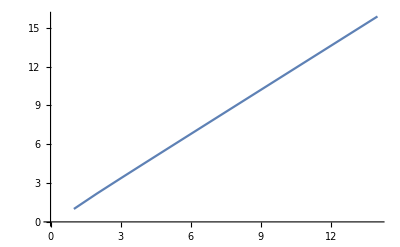

```mathematica
ListLinePlot[{1.,2.2055694304005904,3.3617657267144616,4.506963396530506,5.647874896786514,6.786665803319196,7.92425145292167,9.061086178881702,10.19742128762398,11.333407136290337,12.469139220581782,13.604681115388042,14.74007678842624,15.87535762032022}]
```

### Neumann series

```mathematica
Table[MatrixForm@MatrixPower[cDiffMat[12],m],{m,1,15}]
```

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
-1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(-2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | -2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | -2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -2 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | -2 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | -2 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | -2 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -2 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -2 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -2 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -2),(0 | -3 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 3
3 | 0 | -3 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 3 | 0 | -3 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
-1 | 0 | 3 | 0 | -3 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 3 | 0 | -3 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 3 | 0 | -3 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 3 | 0 | -3 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 3 | 0 | -3 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 3 | 0 | -3 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 3 | 0 | -3 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 3 | 0 | -3
-3 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 3 | 0),(6 | 0 | -4 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -4 | 0
0 | 6 | 0 | -4 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -4
-4 | 0 | 6 | 0 | -4 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | -4 | 0 | 6 | 0 | -4 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | -4 | 0 | 6 | 0 | -4 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | -4 | 0 | 6 | 0 | -4 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | -4 | 0 | 6 | 0 | -4 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | -4 | 0 | 6 | 0 | -4 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | -4 | 0 | 6 | 0 | -4 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | -4 | 0 | 6 | 0 | -4
-4 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -4 | 0 | 6 | 0
0 | -4 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -4 | 0 | 6),(0 | 10 | 0 | -5 | 0 | 1 | 0 | -1 | 0 | 5 | 0 | -10
-10 | 0 | 10 | 0 | -5 | 0 | 1 | 0 | -1 | 0 | 5 | 0
0 | -10 | 0 | 10 | 0 | -5 | 0 | 1 | 0 | -1 | 0 | 5
5 | 0 | -10 | 0 | 10 | 0 | -5 | 0 | 1 | 0 | -1 | 0
0 | 5 | 0 | -10 | 0 | 10 | 0 | -5 | 0 | 1 | 0 | -1
-1 | 0 | 5 | 0 | -10 | 0 | 10 | 0 | -5 | 0 | 1 | 0
0 | -1 | 0 | 5 | 0 | -10 | 0 | 10 | 0 | -5 | 0 | 1
1 | 0 | -1 | 0 | 5 | 0 | -10 | 0 | 10 | 0 | -5 | 0
0 | 1 | 0 | -1 | 0 | 5 | 0 | -10 | 0 | 10 | 0 | -5
-5 | 0 | 1 | 0 | -1 | 0 | 5 | 0 | -10 | 0 | 10 | 0
0 | -5 | 0 | 1 | 0 | -1 | 0 | 5 | 0 | -10 | 0 | 10
10 | 0 | -5 | 0 | 1 | 0 | -1 | 0 | 5 | 0 | -10 | 0),(-20 | 0 | 15 | 0 | -6 | 0 | 2 | 0 | -6 | 0 | 15 | 0
0 | -20 | 0 | 15 | 0 | -6 | 0 | 2 | 0 | -6 | 0 | 15
15 | 0 | -20 | 0 | 15 | 0 | -6 | 0 | 2 | 0 | -6 | 0
0 | 15 | 0 | -20 | 0 | 15 | 0 | -6 | 0 | 2 | 0 | -6
-6 | 0 | 15 | 0 | -20 | 0 | 15 | 0 | -6 | 0 | 2 | 0
0 | -6 | 0 | 15 | 0 | -20 | 0 | 15 | 0 | -6 | 0 | 2
2 | 0 | -6 | 0 | 15 | 0 | -20 | 0 | 15 | 0 | -6 | 0
0 | 2 | 0 | -6 | 0 | 15 | 0 | -20 | 0 | 15 | 0 | -6
-6 | 0 | 2 | 0 | -6 | 0 | 15 | 0 | -20 | 0 | 15 | 0
0 | -6 | 0 | 2 | 0 | -6 | 0 | 15 | 0 | -20 | 0 | 15
15 | 0 | -6 | 0 | 2 | 0 | -6 | 0 | 15 | 0 | -20 | 0
0 | 15 | 0 | -6 | 0 | 2 | 0 | -6 | 0 | 15 | 0 | -20),(0 | -35 | 0 | 21 | 0 | -8 | 0 | 8 | 0 | -21 | 0 | 35
35 | 0 | -35 | 0 | 21 | 0 | -8 | 0 | 8 | 0 | -21 | 0
0 | 35 | 0 | -35 | 0 | 21 | 0 | -8 | 0 | 8 | 0 | -21
-21 | 0 | 35 | 0 | -35 | 0 | 21 | 0 | -8 | 0 | 8 | 0
0 | -21 | 0 | 35 | 0 | -35 | 0 | 21 | 0 | -8 | 0 | 8
8 | 0 | -21 | 0 | 35 | 0 | -35 | 0 | 21 | 0 | -8 | 0
0 | 8 | 0 | -21 | 0 | 35 | 0 | -35 | 0 | 21 | 0 | -8
-8 | 0 | 8 | 0 | -21 | 0 | 35 | 0 | -35 | 0 | 21 | 0
0 | -8 | 0 | 8 | 0 | -21 | 0 | 35 | 0 | -35 | 0 | 21
21 | 0 | -8 | 0 | 8 | 0 | -21 | 0 | 35 | 0 | -35 | 0
0 | 21 | 0 | -8 | 0 | 8 | 0 | -21 | 0 | 35 | 0 | -35
-35 | 0 | 21 | 0 | -8 | 0 | 8 | 0 | -21 | 0 | 35 | 0),(70 | 0 | -56 | 0 | 29 | 0 | -16 | 0 | 29 | 0 | -56 | 0
0 | 70 | 0 | -56 | 0 | 29 | 0 | -16 | 0 | 29 | 0 | -56
-56 | 0 | 70 | 0 | -56 | 0 | 29 | 0 | -16 | 0 | 29 | 0
0 | -56 | 0 | 70 | 0 | -56 | 0 | 29 | 0 | -16 | 0 | 29
29 | 0 | -56 | 0 | 70 | 0 | -56 | 0 | 29 | 0 | -16 | 0
0 | 29 | 0 | -56 | 0 | 70 | 0 | -56 | 0 | 29 | 0 | -16
-16 | 0 | 29 | 0 | -56 | 0 | 70 | 0 | -56 | 0 | 29 | 0
0 | -16 | 0 | 29 | 0 | -56 | 0 | 70 | 0 | -56 | 0 | 29
29 | 0 | -16 | 0 | 29 | 0 | -56 | 0 | 70 | 0 | -56 | 0
0 | 29 | 0 | -16 | 0 | 29 | 0 | -56 | 0 | 70 | 0 | -56
-56 | 0 | 29 | 0 | -16 | 0 | 29 | 0 | -56 | 0 | 70 | 0
0 | -56 | 0 | 29 | 0 | -16 | 0 | 29 | 0 | -56 | 0 | 70),(0 | 126 | 0 | -85 | 0 | 45 | 0 | -45 | 0 | 85 | 0 | -126
-126 | 0 | 126 | 0 | -85 | 0 | 45 | 0 | -45 | 0 | 85 | 0
0 | -126 | 0 | 126 | 0 | -85 | 0 | 45 | 0 | -45 | 0 | 85
85 | 0 | -126 | 0 | 126 | 0 | -85 | 0 | 45 | 0 | -45 | 0
0 | 85 | 0 | -126 | 0 | 126 | 0 | -85 | 0 | 45 | 0 | -45
-45 | 0 | 85 | 0 | -126 | 0 | 126 | 0 | -85 | 0 | 45 | 0
0 | -45 | 0 | 85 | 0 | -126 | 0 | 126 | 0 | -85 | 0 | 45
45 | 0 | -45 | 0 | 85 | 0 | -126 | 0 | 126 | 0 | -85 | 0
0 | 45 | 0 | -45 | 0 | 85 | 0 | -126 | 0 | 126 | 0 | -85
-85 | 0 | 45 | 0 | -45 | 0 | 85 | 0 | -126 | 0 | 126 | 0
0 | -85 | 0 | 45 | 0 | -45 | 0 | 85 | 0 | -126 | 0 | 126
126 | 0 | -85 | 0 | 45 | 0 | -45 | 0 | 85 | 0 | -126 | 0),(-252 | 0 | 211 | 0 | -130 | 0 | 90 | 0 | -130 | 0 | 211 | 0
0 | -252 | 0 | 211 | 0 | -130 | 0 | 90 | 0 | -130 | 0 | 211
211 | 0 | -252 | 0 | 211 | 0 | -130 | 0 | 90 | 0 | -130 | 0
0 | 211 | 0 | -252 | 0 | 211 | 0 | -130 | 0 | 90 | 0 | -130
-130 | 0 | 211 | 0 | -252 | 0 | 211 | 0 | -130 | 0 | 90 | 0
0 | -130 | 0 | 211 | 0 | -252 | 0 | 211 | 0 | -130 | 0 | 90
90 | 0 | -130 | 0 | 211 | 0 | -252 | 0 | 211 | 0 | -130 | 0
0 | 90 | 0 | -130 | 0 | 211 | 0 | -252 | 0 | 211 | 0 | -130
-130 | 0 | 90 | 0 | -130 | 0 | 211 | 0 | -252 | 0 | 211 | 0
0 | -130 | 0 | 90 | 0 | -130 | 0 | 211 | 0 | -252 | 0 | 211
211 | 0 | -130 | 0 | 90 | 0 | -130 | 0 | 211 | 0 | -252 | 0
0 | 211 | 0 | -130 | 0 | 90 | 0 | -130 | 0 | 211 | 0 | -252),(0 | -463 | 0 | 341 | 0 | -220 | 0 | 220 | 0 | -341 | 0 | 463
463 | 0 | -463 | 0 | 341 | 0 | -220 | 0 | 220 | 0 | -341 | 0
0 | 463 | 0 | -463 | 0 | 341 | 0 | -220 | 0 | 220 | 0 | -341
-341 | 0 | 463 | 0 | -463 | 0 | 341 | 0 | -220 | 0 | 220 | 0
0 | -341 | 0 | 463 | 0 | -463 | 0 | 341 | 0 | -220 | 0 | 220
220 | 0 | -341 | 0 | 463 | 0 | -463 | 0 | 341 | 0 | -220 | 0
0 | 220 | 0 | -341 | 0 | 463 | 0 | -463 | 0 | 341 | 0 | -220
-220 | 0 | 220 | 0 | -341 | 0 | 463 | 0 | -463 | 0 | 341 | 0
0 | -220 | 0 | 220 | 0 | -341 | 0 | 463 | 0 | -463 | 0 | 341
341 | 0 | -220 | 0 | 220 | 0 | -341 | 0 | 463 | 0 | -463 | 0
0 | 341 | 0 | -220 | 0 | 220 | 0 | -341 | 0 | 463 | 0 | -463
-463 | 0 | 341 | 0 | -220 | 0 | 220 | 0 | -341 | 0 | 463 | 0),(926 | 0 | -804 | 0 | 561 | 0 | -440 | 0 | 561 | 0 | -804 | 0
0 | 926 | 0 | -804 | 0 | 561 | 0 | -440 | 0 | 561 | 0 | -804
-804 | 0 | 926 | 0 | -804 | 0 | 561 | 0 | -440 | 0 | 561 | 0
0 | -804 | 0 | 926 | 0 | -804 | 0 | 561 | 0 | -440 | 0 | 561
561 | 0 | -804 | 0 | 926 | 0 | -804 | 0 | 561 | 0 | -440 | 0
0 | 561 | 0 | -804 | 0 | 926 | 0 | -804 | 0 | 561 | 0 | -440
-440 | 0 | 561 | 0 | -804 | 0 | 926 | 0 | -804 | 0 | 561 | 0
0 | -440 | 0 | 561 | 0 | -804 | 0 | 926 | 0 | -804 | 0 | 561
561 | 0 | -440 | 0 | 561 | 0 | -804 | 0 | 926 | 0 | -804 | 0
0 | 561 | 0 | -440 | 0 | 561 | 0 | -804 | 0 | 926 | 0 | -804
-804 | 0 | 561 | 0 | -440 | 0 | 561 | 0 | -804 | 0 | 926 | 0
0 | -804 | 0 | 561 | 0 | -440 | 0 | 561 | 0 | -804 | 0 | 926),(0 | 1730 | 0 | -1365 | 0 | 1001 | 0 | -1001 | 0 | 1365 | 0 | -1730
-1730 | 0 | 1730 | 0 | -1365 | 0 | 1001 | 0 | -1001 | 0 | 1365 | 0
0 | -1730 | 0 | 1730 | 0 | -1365 | 0 | 1001 | 0 | -1001 | 0 | 1365
1365 | 0 | -1730 | 0 | 1730 | 0 | -1365 | 0 | 1001 | 0 | -1001 | 0
0 | 1365 | 0 | -1730 | 0 | 1730 | 0 | -1365 | 0 | 1001 | 0 | -1001
-1001 | 0 | 1365 | 0 | -1730 | 0 | 1730 | 0 | -1365 | 0 | 1001 | 0
0 | -1001 | 0 | 1365 | 0 | -1730 | 0 | 1730 | 0 | -1365 | 0 | 1001
1001 | 0 | -1001 | 0 | 1365 | 0 | -1730 | 0 | 1730 | 0 | -1365 | 0
0 | 1001 | 0 | -1001 | 0 | 1365 | 0 | -1730 | 0 | 1730 | 0 | -1365
-1365 | 0 | 1001 | 0 | -1001 | 0 | 1365 | 0 | -1730 | 0 | 1730 | 0
0 | -1365 | 0 | 1001 | 0 | -1001 | 0 | 1365 | 0 | -1730 | 0 | 1730
1730 | 0 | -1365 | 0 | 1001 | 0 | -1001 | 0 | 1365 | 0 | -1730 | 0),(-3460 | 0 | 3095 | 0 | -2366 | 0 | 2002 | 0 | -2366 | 0 | 3095 | 0
0 | -3460 | 0 | 3095 | 0 | -2366 | 0 | 2002 | 0 | -2366 | 0 | 3095
3095 | 0 | -3460 | 0 | 3095 | 0 | -2366 | 0 | 2002 | 0 | -2366 | 0
0 | 3095 | 0 | -3460 | 0 | 3095 | 0 | -2366 | 0 | 2002 | 0 | -2366
-2366 | 0 | 3095 | 0 | -3460 | 0 | 3095 | 0 | -2366 | 0 | 2002 | 0
0 | -2366 | 0 | 3095 | 0 | -3460 | 0 | 3095 | 0 | -2366 | 0 | 2002
2002 | 0 | -2366 | 0 | 3095 | 0 | -3460 | 0 | 3095 | 0 | -2366 | 0
0 | 2002 | 0 | -2366 | 0 | 3095 | 0 | -3460 | 0 | 3095 | 0 | -2366
-2366 | 0 | 2002 | 0 | -2366 | 0 | 3095 | 0 | -3460 | 0 | 3095 | 0
0 | -2366 | 0 | 2002 | 0 | -2366 | 0 | 3095 | 0 | -3460 | 0 | 3095
3095 | 0 | -2366 | 0 | 2002 | 0 | -2366 | 0 | 3095 | 0 | -3460 | 0
0 | 3095 | 0 | -2366 | 0 | 2002 | 0 | -2366 | 0 | 3095 | 0 | -3460),(0 | -6555 | 0 | 5461 | 0 | -4368 | 0 | 4368 | 0 | -5461 | 0 | 6555
6555 | 0 | -6555 | 0 | 5461 | 0 | -4368 | 0 | 4368 | 0 | -5461 | 0
0 | 6555 | 0 | -6555 | 0 | 5461 | 0 | -4368 | 0 | 4368 | 0 | -5461
-5461 | 0 | 6555 | 0 | -6555 | 0 | 5461 | 0 | -4368 | 0 | 4368 | 0
0 | -5461 | 0 | 6555 | 0 | -6555 | 0 | 5461 | 0 | -4368 | 0 | 4368
4368 | 0 | -5461 | 0 | 6555 | 0 | -6555 | 0 | 5461 | 0 | -4368 | 0
0 | 4368 | 0 | -5461 | 0 | 6555 | 0 | -6555 | 0 | 5461 | 0 | -4368
-4368 | 0 | 4368 | 0 | -5461 | 0 | 6555 | 0 | -6555 | 0 | 5461 | 0
0 | -4368 | 0 | 4368 | 0 | -5461 | 0 | 6555 | 0 | -6555 | 0 | 5461
5461 | 0 | -4368 | 0 | 4368 | 0 | -5461 | 0 | 6555 | 0 | -6555 | 0
0 | 5461 | 0 | -4368 | 0 | 4368 | 0 | -5461 | 0 | 6555 | 0 | -6555
-6555 | 0 | 5461 | 0 | -4368 | 0 | 4368 | 0 | -5461 | 0 | 6555 | 0)}

```mathematica
idPluscDiffMat[7]//MatrixForm
```

(1 | ν | 0 | 0 | 0 | 0 | -ν
-ν | 1 | ν | 0 | 0 | 0 | 0
0 | -ν | 1 | ν | 0 | 0 | 0
0 | 0 | -ν | 1 | ν | 0 | 0
0 | 0 | 0 | -ν | 1 | ν | 0
0 | 0 | 0 | 0 | -ν | 1 | ν
ν | 0 | 0 | 0 | 0 | -ν | 1)

```mathematica
idPluscDiffMat[7]//Eigenvalues//Union
```

```mathematica
1-√(1+Root[1+7 ν^2+14 ν^4+7 ν^6+(3+14 ν^2+14 ν^4) #1+(3+7 ν^2) #1^2+#1^3&,1])/.ν->16.
```

1.-31.1977 ⅈ

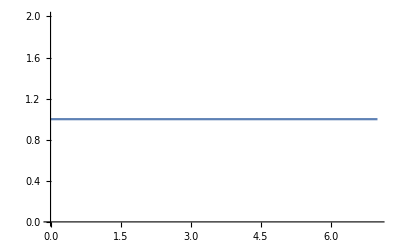

```mathematica
Plot[{1,1-√(1+Root[1+7 ν^2+14 ν^4+7 ν^6+(3+14 ν^2+14 ν^4) #1+(3+7 ν^2) #1^2+#1^3&,1]),1+√(1+Root[1+7 ν^2+14 ν^4+7 ν^6+(3+14 ν^2+14 ν^4) #1+(3+7 ν^2) #1^2+#1^3&,1]),1-√(1+Root[1+7 ν^2+14 ν^4+7 ν^6+(3+14 ν^2+14 ν^4) #1+(3+7 ν^2) #1^2+#1^3&,2]),1+√(1+Root[1+7 ν^2+14 ν^4+7 ν^6+(3+14 ν^2+14 ν^4) #1+(3+7 ν^2) #1^2+#1^3&,2]),1-√(1+Root[1+7 ν^2+14 ν^4+7 ν^6+(3+14 ν^2+14 ν^4) #1+(3+7 ν^2) #1^2+#1^3&,3]),1+√(1+Root[1+7 ν^2+14 ν^4+7 ν^6+(3+14 ν^2+14 ν^4) #1+(3+7 ν^2) #1^2+#1^3&,3])},{ν,0,7}]
```

### A formula for the inverse of the circulant matrix:

```mathematica
With[{m=12},IdentityMatrix[m]+ν cDiffMat[m]]//MatrixForm
```

(1 | ν | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ν
-ν | 1 | ν | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ν | 1 | ν | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ν | 1 | ν | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ν | 1 | ν | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ν | 1 | ν | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ν | 1 | ν | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ν | 1 | ν | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ν | 1 | ν | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ν | 1 | ν | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ν | 1 | ν
ν | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ν | 1)

### The λ_j quantities:

```mathematica
1+ν Exp[(2π I)/n j]-ν Exp[(2π I)/n j(n-1)]
```

```mathematica
1+ⅇ^((2 ⅈ j π)/n) ν-ⅇ^((2 ⅈ j (-1+n) π)/n) ν//ComplexExpand//TrigReduce
```

```mathematica
1+ν (-2 Sin[-(j (-2+n) π)/n] Sin[j π])+ⅈ ν (2 Cos[j π] Sin[-(j (-2+n) π)/n])
```

1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n]

```mathematica
1+(-I 2 ν ( ⅇ^(ⅈ j π)) Sin[(j (-2+n) π)/n])
```

```mathematica
1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]==1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n]//Simplify
```

True

Check:

```mathematica
idPluscDiffMat[7]/.ν->E//Eigenvalues//Sort//RootReduce
```

{1,1-√(1+Root[1+7 ⅇ^2+14 ⅇ^4+7 ⅇ^6+(3+14 ⅇ^2+14 ⅇ^4) #1+(3+7 ⅇ^2) #1^2+#1^3&,1]),1+√(1+Root[1+7 ⅇ^2+14 ⅇ^4+7 ⅇ^6+(3+14 ⅇ^2+14 ⅇ^4) #1+(3+7 ⅇ^2) #1^2+#1^3&,1]),1-√(1+Root[1+7 ⅇ^2+14 ⅇ^4+7 ⅇ^6+(3+14 ⅇ^2+14 ⅇ^4) #1+(3+7 ⅇ^2) #1^2+#1^3&,2]),1+√(1+Root[1+7 ⅇ^2+14 ⅇ^4+7 ⅇ^6+(3+14 ⅇ^2+14 ⅇ^4) #1+(3+7 ⅇ^2) #1^2+#1^3&,2]),1-√(1+Root[1+7 ⅇ^2+14 ⅇ^4+7 ⅇ^6+(3+14 ⅇ^2+14 ⅇ^4) #1+(3+7 ⅇ^2) #1^2+#1^3&,3]),1+√(1+Root[1+7 ⅇ^2+14 ⅇ^4+7 ⅇ^6+(3+14 ⅇ^2+14 ⅇ^4) #1+(3+7 ⅇ^2) #1^2+#1^3&,3])}

```mathematica
With[{n=7,ν=E},Table[1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n],{j,0,n-1}]]//Sort
```

{1,1-2 ⅈ ⅇ Cos[π/14],1+2 ⅈ ⅇ Cos[π/14],1-2 ⅈ ⅇ Cos[(3 π)/14],1+2 ⅈ ⅇ Cos[(3 π)/14],1-2 ⅈ ⅇ Sin[π/7],1+2 ⅈ ⅇ Sin[π/7]}

```mathematica
1-√(1+Root[1+7 ⅇ^2+14 ⅇ^4+7 ⅇ^6+(3+14 ⅇ^2+14 ⅇ^4) #1+(3+7 ⅇ^2) #1^2+#1^3&,1])-(1-2 ⅈ ⅇ Cos[π/14])//FullSimplify
```

# The a_k quantities (i.e., the row vectors of the inverse matrix, which is also circulant):

```mathematica
1/n Sum[(1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n])^-1 Exp[-(2π I)/n j k],{j,0,n-1}]
```

(∑_(j=0)^(-1+n) ⅇ^(-(2 ⅈ j k π)/n)/(1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n]))/n

```mathematica
Product[1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n],{j,0,n-1}]
```

∏_(j=0)^(-1+n) (1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n])

```mathematica
Product[1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n],{j,0,n-1},Assumptions->{n>2&&n∈Integers}]
```

Product[1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n],{j,0,-1+n},Assumptions→{n>2&&n∈Integers}]

```mathematica
With[{n=6},Product[1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n],{j,0,n-1}]]//Expand
```

1+6 ν^2+9 ν^4

# Notice that in the 2012 manuscript by Bozkurt, the exponent “-1” is missing !!!

```mathematica
With[{n=6},Table[1/n Sum[(1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n])^-1 Exp[-(2π I)/n j k],{j,0,n-1}],{k,0,n-1}]]//Simplify
```

{(1+ν^2)/(1+3 ν^2),-ν/(1+3 ν^2),ν^2/(1+3 ν^2),0,ν^2/(1+3 ν^2),ν/(1+3 ν^2)}

#### The first row of the circulant matrix multiplied by the determinant:

```mathematica
Product[1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n],{j,0,n-1}]/n Sum[(1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n])^-1 Exp[-(2π I)/n j k],{j,0,n-1}]
```

((∏_(j=0)^(-1+n) (1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n])) ∑_(j=0)^(-1+n) ⅇ^(-(2 ⅈ j k π)/n)/(1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n]))/n

# The first row of the circulant matrix (without the determinant): it is in simplified form

```mathematica
With[{n=8},Table[1/n Sum[(1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n])^-1 Exp[-(2π I)/n j k],{j,0,n-1}],{k,0,n-1}]]//Simplify
```

{(1+4 ν^2+2 ν^4)/(1+6 ν^2+8 ν^4),-(ν+3 ν^3)/(1+6 ν^2+8 ν^4),ν^2/(1+4 ν^2),-ν^3/(1+6 ν^2+8 ν^4),(2 ν^4)/(1+6 ν^2+8 ν^4),ν^3/(1+6 ν^2+8 ν^4),ν^2/(1+4 ν^2),(ν+3 ν^3)/(1+6 ν^2+8 ν^4)}

```mathematica
det[8]
```

1+8 ν^2+20 ν^4+16 ν^6

#### This form is not simplified:

```mathematica
inverse[8][[1]]
```

{(1+6 ν^2+10 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν-5 ν^3-6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν^3-2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(2 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^3+2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν+5 ν^3+6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6)}

```mathematica
inverse[8][[1]]//Simplify
```

{(1+4 ν^2+2 ν^4)/(1+6 ν^2+8 ν^4),-(ν+3 ν^3)/(1+6 ν^2+8 ν^4),ν^2/(1+4 ν^2),-ν^3/(1+6 ν^2+8 ν^4),(2 ν^4)/(1+6 ν^2+8 ν^4),ν^3/(1+6 ν^2+8 ν^4),ν^2/(1+4 ν^2),(ν+3 ν^3)/(1+6 ν^2+8 ν^4)}

### Find some recurrence relations among these polynomials/rational functions.

```mathematica
With[{m=2},(det[m] Inverse[IdentityMatrix[m]+ν cDiffMat[m]])//First]
```

{1,-ν}

```mathematica
With[{m=3},(det[m] Inverse[IdentityMatrix[m]+ν cDiffMat[m]])//First]
```

{1+ν^2,-ν+ν^2,ν+ν^2}

```mathematica
With[{m=4},(det[m] Inverse[IdentityMatrix[m]+ν cDiffMat[m]])//First]
```

{1+2 ν^2,-ν,2 ν^2,ν}

```mathematica
With[{m=5},(det[m] Inverse[IdentityMatrix[m]+ν cDiffMat[m]])//First]
```

{1+3 ν^2+ν^4,-ν-2 ν^3+ν^4,ν^2+ν^3+ν^4,ν^2-ν^3+ν^4,ν+2 ν^3+ν^4}

```mathematica
With[{m=6},(det[m] Inverse[IdentityMatrix[m]+ν cDiffMat[m]])//First]
```

{1+4 ν^2+3 ν^4,-ν-3 ν^3,ν^2+3 ν^4,0,ν^2+3 ν^4,ν+3 ν^3}

```mathematica
With[{m=7},(det[m] Inverse[IdentityMatrix[m]+ν cDiffMat[m]])//First]
```

{1+5 ν^2+6 ν^4+ν^6,-ν-4 ν^3-3 ν^5+ν^6,ν^2+3 ν^4+ν^5+ν^6,-ν^3+ν^4-2 ν^5+ν^6,ν^3+ν^4+2 ν^5+ν^6,ν^2+3 ν^4-ν^5+ν^6,ν+4 ν^3+3 ν^5+ν^6}

```mathematica
With[{m=8},(det[m] Inverse[IdentityMatrix[m]+ν cDiffMat[m]])//First]
```

{1+6 ν^2+10 ν^4+4 ν^6,-ν-5 ν^3-6 ν^5,ν^2+4 ν^4+4 ν^6,-ν^3-2 ν^5,2 ν^4+4 ν^6,ν^3+2 ν^5,ν^2+4 ν^4+4 ν^6,ν+5 ν^3+6 ν^5}

```mathematica
With[{m=9},(det[m] Inverse[IdentityMatrix[m]+ν cDiffMat[m]])//First]
```

{1+7 ν^2+15 ν^4+10 ν^6+ν^8,-ν-6 ν^3-10 ν^5-4 ν^7+ν^8,ν^2+5 ν^4+6 ν^6+ν^7+ν^8,-ν^3-4 ν^5+ν^6-3 ν^7+ν^8,ν^4+ν^5+3 ν^6+2 ν^7+ν^8,ν^4-ν^5+3 ν^6-2 ν^7+ν^8,ν^3+4 ν^5+ν^6+3 ν^7+ν^8,ν^2+5 ν^4+6 ν^6-ν^7+ν^8,ν+6 ν^3+10 ν^5+4 ν^7+ν^8}

### The (1,1) elements of the sequence of odd matrices satisfy the linear recursion:

```mathematica
FindLinearRecurrence[{1+ν^2,1+3 ν^2+ν^4,1+5 ν^2+6 ν^4+ν^6,1+7 ν^2+15 ν^4+10 ν^6+ν^8,1+9 ν^2+28 ν^4+35 ν^6+15 ν^8+ν^10,1+11 ν^2+45 ν^4+84 ν^6+70 ν^8+21 ν^10+ν^12,1+13 ν^2+66 ν^4+165 ν^6+210 ν^8+126 ν^10+28 ν^12+ν^14,1+15 ν^2+91 ν^4+286 ν^6+495 ν^8+462 ν^10+210 ν^12+36 ν^14+ν^16,1+17 ν^2+120 ν^4+455 ν^6+1001 ν^8+1287 ν^10+924 ν^12+330 ν^14+45 ν^16+ν^18,1+19 ν^2+153 ν^4+680 ν^6+1820 ν^8+3003 ν^10+3003 ν^12+1716 ν^14+495 ν^16+55 ν^18+ν^20}]
```

{1+2 ν^2,-ν^4}

```mathematica
RecurrenceTable[{P[n+2]==(1+2 ν^2)P[n+1]-ν^4 P[n],P[1]==1,P[2]==1+ν^2},P,{n,1,10}]//Expand
```

{1,1+ν^2,1+3 ν^2+ν^4,1+5 ν^2+6 ν^4+ν^6,1+7 ν^2+15 ν^4+10 ν^6+ν^8,1+9 ν^2+28 ν^4+35 ν^6+15 ν^8+ν^10,1+11 ν^2+45 ν^4+84 ν^6+70 ν^8+21 ν^10+ν^12,1+13 ν^2+66 ν^4+165 ν^6+210 ν^8+126 ν^10+28 ν^12+ν^14,1+15 ν^2+91 ν^4+286 ν^6+495 ν^8+462 ν^10+210 ν^12+36 ν^14+ν^16,1+17 ν^2+120 ν^4+455 ν^6+1001 ν^8+1287 ν^10+924 ν^12+330 ν^14+45 ν^16+ν^18}

### The (1,3) elements (for odd matrix sizes) satisfy the 3rd-degree linear recursion:

```mathematica
Table[First[(det[m] Inverse[IdentityMatrix[m]+ν cDiffMat[m]])][[2]],{m,3,17,2}]//Simplify//Expand
```

{-ν+ν^2,-ν-2 ν^3+ν^4,-ν-4 ν^3-3 ν^5+ν^6,-ν-6 ν^3-10 ν^5-4 ν^7+ν^8,-ν-8 ν^3-21 ν^5-20 ν^7-5 ν^9+ν^10,-ν-10 ν^3-36 ν^5-56 ν^7-35 ν^9-6 ν^11+ν^12,-ν-12 ν^3-55 ν^5-120 ν^7-126 ν^9-56 ν^11-7 ν^13+ν^14,-ν-14 ν^3-78 ν^5-220 ν^7-330 ν^9-252 ν^11-84 ν^13-8 ν^15+ν^16}

```mathematica
FindLinearRecurrence[{-ν+ν^2,-ν-2 ν^3+ν^4,-ν-4 ν^3-3 ν^5+ν^6,-ν-6 ν^3-10 ν^5-4 ν^7+ν^8,-ν-8 ν^3-21 ν^5-20 ν^7-5 ν^9+ν^10,-ν-10 ν^3-36 ν^5-56 ν^7-35 ν^9-6 ν^11+ν^12,-ν-12 ν^3-55 ν^5-120 ν^7-126 ν^9-56 ν^11-7 ν^13+ν^14,-ν-14 ν^3-78 ν^5-220 ν^7-330 ν^9-252 ν^11-84 ν^13-8 ν^15+ν^16}]
```

{1+3 ν^2,-ν^2-3 ν^4,ν^6}

```mathematica
RecurrenceTable[{P[n+3]==(1+3 ν^2)P[n+2]-ν^2 (1+3 ν^2)P[n+1]+ν^6 P[n],P[1]==-ν+ν^2,P[2]==-ν-2 ν^3+ν^4,P[3]==-ν-4 ν^3-3 ν^5+ν^6},P,{n,1,8}]//Expand
```

{-ν+ν^2,-ν-2 ν^3+ν^4,-ν-4 ν^3-3 ν^5+ν^6,-ν-6 ν^3-10 ν^5-4 ν^7+ν^8,-ν-8 ν^3-21 ν^5-20 ν^7-5 ν^9+ν^10,-ν-10 ν^3-36 ν^5-56 ν^7-35 ν^9-6 ν^11+ν^12,-ν-12 ν^3-55 ν^5-120 ν^7-126 ν^9-56 ν^11-7 ν^13+ν^14,-ν-14 ν^3-78 ν^5-220 ν^7-330 ν^9-252 ν^11-84 ν^13-8 ν^15+ν^16}

```mathematica
RecurrenceTable[{P[n+3]==(1+3 ν^2)P[n+2]-ν^2 (1+3 ν^2)P[n+1]+ν^6 P[n],P[1]==-ν+ν^2,P[2]==-ν-2 ν^3+ν^4,P[3]==-ν-4 ν^3-3 ν^5+ν^6},P,{n,1,10}]
```

# Seeking recursion among det(I + ν A) for odd matrix sizes

```mathematica
det[1]
```

SparseArray::bndstd: The starting position {1,2} for the band Band[{1,2}] is not an explicit element position in an array with dimensions {1,1}.

1+ν SparseArray[{Band[{1,2}]→1,Band[{2,1}]→-1,Band[{1,1}]→-1,Band[{1,1}]→1},{1,1}]

```mathematica
det[3]
```

1+3 ν^2

```mathematica
idPluscDiffMat[5]//MatrixForm
```

(1 | ν | 0 | 0 | -ν
-ν | 1 | ν | 0 | 0
0 | -ν | 1 | ν | 0
0 | 0 | -ν | 1 | ν
ν | 0 | 0 | -ν | 1)

```mathematica
Det@({{1, ν, 0, 0, -ν}, {-ν, 1, ν, 0, 0}, {0, -ν, 1, ν, 0}, {0, 0, -ν, 1, ν}, {-ν, 0, 0, -ν, 1}})-Det@({{1, ν, 0, 0, 0}, {-ν, 1, ν, 0, 0}, {0, -ν, 1, ν, 0}, {0, 0, -ν, 1, ν}, {0, 0, 0, -ν, 1}})
```

-ν^2-2 ν^4-2 ν^5

```mathematica
Det@({{1, ν, 0, 0, 0, 0, -ν}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {ν, 0, 0, 0, 0, -ν, 1}})-Det@({{1, ν, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}})
```

ν^2+4 ν^4+3 ν^6

```mathematica
With[{n=4},det[2n+5]==(1+2 ν^2)det[2n+3]-ν^4 det[2n+1]]
```

1+13 ν^2+65 ν^4+156 ν^6+182 ν^8+91 ν^10+13 ν^12==-ν^4 (1+9 ν^2+27 ν^4+30 ν^6+9 ν^8)+(1+2 ν^2) (1+11 ν^2+44 ν^4+77 ν^6+55 ν^8+11 ν^10)

```mathematica
Table[det[m],{m,3,11,2}]//Simplify//Expand
```

{1+3 ν^2,1+5 ν^2+5 ν^4,1+7 ν^2+14 ν^4+7 ν^6,1+9 ν^2+27 ν^4+30 ν^6+9 ν^8,1+11 ν^2+44 ν^4+77 ν^6+55 ν^8+11 ν^10}

```mathematica
FindLinearRecurrence[{1+3 ν^2,1+5 ν^2+5 ν^4,1+7 ν^2+14 ν^4+7 ν^6,1+9 ν^2+27 ν^4+30 ν^6+9 ν^8,1+11 ν^2+44 ν^4+77 ν^6+55 ν^8+11 ν^10}]
```

{1+2 ν^2,-ν^4}

```mathematica
RecurrenceTable[{De[n+2]==(1+2 ν^2)De[n+1]-ν^4 De[n],De[1]==1,De[2]==1+3 ν^2},De,{n,2,6}]//Expand
```

{1+3 ν^2,1+5 ν^2+5 ν^4,1+7 ν^2+14 ν^4+7 ν^6,1+9 ν^2+27 ν^4+30 ν^6+9 ν^8,1+11 ν^2+44 ν^4+77 ν^6+55 ν^8+11 ν^10}

```mathematica
RSolve[{De[n+2]==(1+2 ν^2)De[n+1]-ν^4 De[n]},De[n],n]
```

{{De[n]→2^-n (1+2 ν^2-√(1+4 ν^2))^n C[1]+2^-n (1+2 ν^2+√(1+4 ν^2))^n C[2]}}

```mathematica
Reduce[1+2 ν^2-√(1+4 ν^2)≥0]
```

ν∈Reals

If C[1]>0 && C[2]>0, this means that all determinants are positive for positive ν>0.

#### With starting values:

```mathematica
RSolve[{De[n+2]==(1+2 ν^2)De[n+1]-ν^4 De[n],De[1]==1,De[2]==1+3 ν^2},De[n],n]
```

{{De[n]→-1/(ν^2 √(1+4 ν^2))2^(-1-n) ((1+2 ν^2-√(1+4 ν^2))^n+4 ν^2 (1+2 ν^2-√(1+4 ν^2))^n+√(1+4 ν^2) (1+2 ν^2-√(1+4 ν^2))^n-(1+2 ν^2+√(1+4 ν^2))^n-4 ν^2 (1+2 ν^2+√(1+4 ν^2))^n+√(1+4 ν^2) (1+2 ν^2+√(1+4 ν^2))^n)}}

```mathematica
FullSimplify[-1/(ν^2 √(1+4 ν^2))2^(-1-n) ((1+2 ν^2-√(1+4 ν^2))^n+4 ν^2 (1+2 ν^2-√(1+4 ν^2))^n+√(1+4 ν^2) (1+2 ν^2-√(1+4 ν^2))^n-(1+2 ν^2+√(1+4 ν^2))^n-4 ν^2 (1+2 ν^2+√(1+4 ν^2))^n+√(1+4 ν^2) (1+2 ν^2+√(1+4 ν^2))^n),ν>0]
```

```mathematica
-(2^(-1-n) ((1+2 ν^2-√(1+4 ν^2))^n+√(1+4 ν^2) (1+2 ν^2-√(1+4 ν^2))^n+(1+2 ν^2+√(1+4 ν^2))^n-√(1+4 ν^2) (1+2 ν^2+√(1+4 ν^2))^n))/ν^2
```

```mathematica
-(2^(-1-n) ((1+2 ν^2-√(1+4 ν^2))^n (1+√(1+4 ν^2))+-(-1+√(1+4 ν^2)) (1+2 ν^2+√(1+4 ν^2))^n))/ν^2
```

```mathematica
Table[-(2^(-1-n) ((1+2 ν^2-√(1+4 ν^2))^n (1+√(1+4 ν^2))+(1-√(1+4 ν^2)) (1+2 ν^2+√(1+4 ν^2))^n))/ν^2,{n,2,6}]//Simplify
```

{1+3 ν^2,1+5 ν^2+5 ν^4,1+7 ν^2+14 ν^4+7 ν^6,1+9 ν^2+27 ν^4+30 ν^6+9 ν^8,1+11 ν^2+44 ν^4+77 ν^6+55 ν^8+11 ν^10}

```mathematica
RecurrenceTable[{De[n+2]==(1+2 ν^2)De[n+1]-ν^4 De[n],De[1]==1,De[2]==1+3 ν^2},De,{n,2,6}]//Expand
```

{1+3 ν^2,1+5 ν^2+5 ν^4,1+7 ν^2+14 ν^4+7 ν^6,1+9 ν^2+27 ν^4+30 ν^6+9 ν^8,1+11 ν^2+44 ν^4+77 ν^6+55 ν^8+11 ν^10}

### We need to prove non-negativity of -(2^(-1-n) ((1+2 ν^2-√(1+4 ν^2))^n (1+√(1+4 ν^2))+(1-√(1+4 ν^2)) (1+2 ν^2+√(1+4 ν^2))^n))/ν^2

### That is: that of

```mathematica
(1+2 ν^2-√(1+4 ν^2))^n (-1-√(1+4 ν^2))+(-1+√(1+4 ν^2)) (1+2 ν^2+√(1+4 ν^2))^n≥0
```

```mathematica
+(-1+√(1+4 ν^2)) (1+2 ν^2+√(1+4 ν^2))^n≥(+1+√(1+4 ν^2)) (1+2 ν^2-√(1+4 ν^2))^n
```

```mathematica
((-1+√(1+4 ν^2))/(1+√(1+4 ν^2))) ≥((1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2)))^n
```

```mathematica
Table[(1+2 ν^2-√(1+4 ν^2))/(2 ν^2)≥((1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2)))^n,{n,1,3}]
```

{(1+2 ν^2-√(1+4 ν^2))/(2 ν^2)≥(1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2)),(1+2 ν^2-√(1+4 ν^2))/(2 ν^2)≥((1+2 ν^2-√(1+4 ν^2))^2)/((1+2 ν^2+√(1+4 ν^2))^2),(1+2 ν^2-√(1+4 ν^2))/(2 ν^2)≥((1+2 ν^2-√(1+4 ν^2))^3)/((1+2 ν^2+√(1+4 ν^2))^3)}

For n=1, this is true. But the RHS is a strictly decreasing function in n. Non-negativity hence follows (provided we establish the recursive relationship for the determinants).